```mathematica
path = "/home/agarcia_pc/Programming_pc/Bioinformatica/ICGC/results/to-plot"
```

/home/agarcia_pc/Programming_pc/Bioinformatica/ICGC/results/to-plot

```mathematica
file = "-.plot.tsv"
```

-.plot.tsv

```mathematica
plotName = "AllProjects&AllGenes"
```

AllProjects&AllGenes

```mathematica
filename = StringReplace["path/file", {"path" -> path, "file" -> #}] &
```

StringReplace[path/file,{path→path,file→#1}]&

```mathematica
data = Import[filename[file]][[2;;]]
```

{{1,43637911},{2,2316229},{3,328046},{4,90285},{5,31236},{6,12826},{7,5876},{8,2945},{9,1603},{10,928},{11,598},{12,383},{13,261},{14,183},{15,129},{16,100},{17,81},{18,54},{19,54},{20,21},{21,31},{22,33},{23,16},{24,13},{25,13},{26,14},{27,14},{28,10},{29,7},{30,7},{31,8},{32,8},{33,5},{34,3},{35,4},{36,4},{38,3},{39,3},{40,5},{41,2},{43,5},{44,4},{45,2},{46,1},{47,1},{49,1},{50,2},{52,1},{54,1},{55,1},{56,1},{59,1},{63,1},{66,1},{67,2},{71,1},{72,1},{78,1},{81,1},{87,1},{90,1},{93,1},{101,1},{112,1},{114,2},{131,1},{140,1},{216,1},{220,1},{236,1},{257,1},{263,1},{352,1},{542,1}}

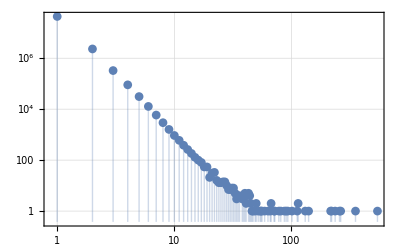

```mathematica
LogLogLegended =
ListLogLogPlot[data, PlotTheme->"Detailed", Joined -> False, PlotMarkers-> Automatic, Filling->Bottom, PlotLegends-> plotName]
(*LLLname = StringReplace["LogLog-PlotName-Legended.png", {"PlotName"-> "AllProjects&AllGenes"}]
Export[filename[LLLname], LogLogLegended]*)
```

```mathematica
data[[1]]
```

{1,43637911}

```mathematica
data[[45]]
```

{47,1}

```mathematica
fit = NonlinearModelFit[data[[;;45]], A x^B,{A,B},x]
```

FittedModel[(4.36385×10^7)/x^4.25256]

```mathematica
Normal[fit]
```

(4.36385×10^7)/x^4.25256

```mathematica
fitString = StringReplace["y = A*x^B", {"A"->#1, "B"->#2}] &
```

StringReplace[y = A*x^B,{A→#1,B→#2}]&

```mathematica
fit["ParameterErrors"]
```

{13968.8,0.00842797}

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 4.36385×10^7 | 13968.8 | 3124. | 8.50466×10^-117
B | -4.25256 | 0.00842797 | -504.577 | 9.43698×10^-83

```mathematica
fit["AdjustedRSquared"]
```

0.999995

```mathematica
fit["BestFitParameters"]
```

{A→4.36385×10^7,B→-4.25256}

```mathematica
fitString[fit["BestFitParameters"][["A"]], fit["BestFitParameters"][["B"]] ]
```

Part::pspec1: Part specification A is not applicable.

Part::pspec1: Part specification B is not applicable.

Part::pspec1: Part specification A is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

y = ~~{A→4.36385×10^7,B→-4.25256}⟦A⟧~~*x^~~{A→4.36385×10^7,B→-4.25256}⟦B⟧

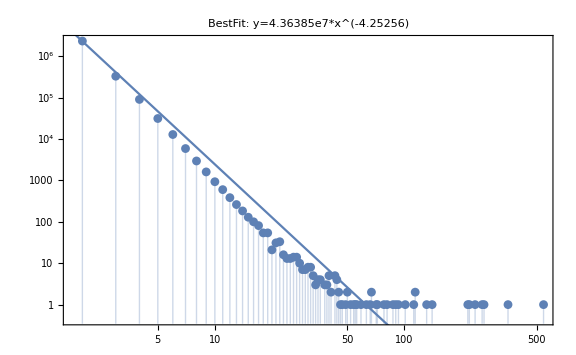

```mathematica
loglogFitPlot = Show[
ListLogLogPlot[data[[2;;]], Filling -> Axis],
LogLogPlot[fit[x],{x,1,542}],
Frame->True,
ImageSize->Large,
PlotLabel -> "BestFit: y=4.36385e7*x^(-4.25256)"
]
```

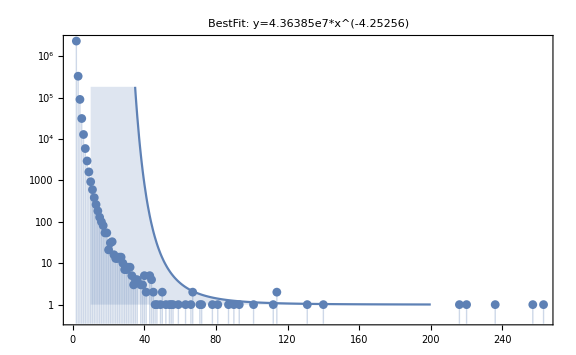

```mathematica
fitPlot = Show[
ListLogPlot[data[[2;;72]], Filling -> Axis],
Plot[fit[x],{x,10,200}, Filling ->Axis],
Frame->True,
ImageSize -> Large,
PlotLabel -> "BestFit: y=4.36385e7*x^(-4.25256)"
]
```

```mathematica
fit["FitResiduals"]
```

{-553.12,26832.9,-80162.5,-29823.1,-15264.4,-8589.76,-5242.3,-3356.21,-2215.52,-1511.54,-1028.61,-740.531,-538.387,-400.297,-305.98,-230.579,-174.452,-146.33,-105.181,-106.985,-73.0042,-52.3365,-54.638,-45.9436,-36.55,-27.9381,-21.7197,-20.6014,-19.3592,-15.8203,-11.8501,-9.34311,-10.2158,-10.4017,-7.84746,-6.50988,-5.35108,-4.47773,-1.71446,-4.04515,0.0632099,-0.47699,-2.06895,-2.70587,-2.38198}

```mathematica
ListPlot[%206]
```

Out::intm: Machine-sized integer expected at position 1 in Out[206.].

ListPlot::lpn: Out[206.] is not a list of numbers or pairs of numbers.

ListPlot[%206]

```mathematica
Total[%206]
```

206

```mathematica
Total[%194]
```

194

```mathematica
Histogram[%103]
```

Out::intm: Machine-sized integer expected at position 1 in Out[103.].

Histogram::ldata: %103 is not a valid dataset or list of datasets.

Histogram[%103]

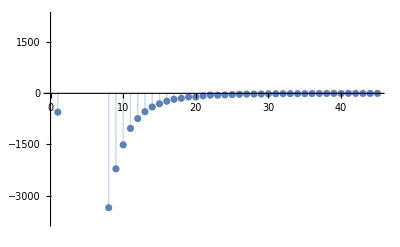

```mathematica
ListPlot[fit["FitResiduals"],Filling->Axis]
```

```mathematica
Remove[minimize]
```

```mathematica
minimize[data_, i0_] := 
Module[{i,fit,totalError, minValue = Infinity,min = i0, errors = {Nothing}},
For[i=min,i< Length[data], i = i+1, 
fit = NonlinearModelFit[data[[;;i]], A x^B,{A,B},x];
totalError = Abs[Total[fit["FitResiduals"]]];
errors = Append[errors, {i,totalError}];
If[totalError < minValue, min = i; minValue = totalError, Nothing];
Print[StringReplace["i:_i, error:_totalError, minimum:_minValue", {"_i"->i, "_totalError"->totalError, "_minValue"->minValue}]];
];
{min, errors}
]
```

```mathematica
m = minimize[data, 20]
```

i:~~20~~, error:~~123663.~~, minimum:~~123663.

i:~~21~~, error:~~123736.~~, minimum:~~123663.

i:~~22~~, error:~~123788.~~, minimum:~~123663.

i:~~23~~, error:~~123843.~~, minimum:~~123663.

i:~~24~~, error:~~123889.~~, minimum:~~123663.

i:~~25~~, error:~~123925.~~, minimum:~~123663.

i:~~26~~, error:~~123953.~~, minimum:~~123663.

i:~~27~~, error:~~123975.~~, minimum:~~123663.

i:~~28~~, error:~~123996.~~, minimum:~~123663.

i:~~29~~, error:~~124015.~~, minimum:~~123663.

i:~~30~~, error:~~124031.~~, minimum:~~123663.

i:~~31~~, error:~~124043.~~, minimum:~~123663.

i:~~32~~, error:~~124052.~~, minimum:~~123663.

i:~~33~~, error:~~124062.~~, minimum:~~123663.

i:~~34~~, error:~~124073.~~, minimum:~~123663.

i:~~35~~, error:~~124080.~~, minimum:~~123663.

i:~~36~~, error:~~124087.~~, minimum:~~123663.

i:~~37~~, error:~~124092.~~, minimum:~~123663.

i:~~38~~, error:~~124097.~~, minimum:~~123663.

i:~~39~~, error:~~124099.~~, minimum:~~123663.

i:~~40~~, error:~~124103.~~, minimum:~~123663.

i:~~41~~, error:~~124103.~~, minimum:~~123663.

i:~~42~~, error:~~124103.~~, minimum:~~123663.

i:~~43~~, error:~~124105.~~, minimum:~~123663.

i:~~44~~, error:~~124108.~~, minimum:~~123663.

i:~~45~~, error:~~124110.~~, minimum:~~123663.

i:~~46~~, error:~~124112.~~, minimum:~~123663.

i:~~47~~, error:~~124113.~~, minimum:~~123663.

i:~~48~~, error:~~124114.~~, minimum:~~123663.

i:~~49~~, error:~~2.79206×10^6~~, minimum:~~123663.

i:~~50~~, error:~~124115.~~, minimum:~~123663.

i:~~51~~, error:~~124116.~~, minimum:~~123663.

i:~~52~~, error:~~124116.~~, minimum:~~123663.

i:~~53~~, error:~~2.79206×10^6~~, minimum:~~123663.

i:~~54~~, error:~~2.79206×10^6~~, minimum:~~123663.

i:~~55~~, error:~~124115.~~, minimum:~~123663.

i:~~56~~, error:~~124114.~~, minimum:~~123663.

i:~~57~~, error:~~124114.~~, minimum:~~123663.

i:~~58~~, error:~~2.79207×10^6~~, minimum:~~123663.

i:~~59~~, error:~~124113.~~, minimum:~~123663.

i:~~60~~, error:~~124112.~~, minimum:~~123663.

i:~~61~~, error:~~124111.~~, minimum:~~123663.

i:~~62~~, error:~~124110.~~, minimum:~~123663.

i:~~63~~, error:~~124109.~~, minimum:~~123663.

i:~~64~~, error:~~2.79208×10^6~~, minimum:~~123663.

i:~~65~~, error:~~2.79208×10^6~~, minimum:~~123663.

i:~~66~~, error:~~124106.~~, minimum:~~123663.

i:~~67~~, error:~~124105.~~, minimum:~~123663.

i:~~68~~, error:~~124104.~~, minimum:~~123663.

i:~~69~~, error:~~2.79208×10^6~~, minimum:~~123663.

i:~~70~~, error:~~2.79208×10^6~~, minimum:~~123663.

i:~~71~~, error:~~124101.~~, minimum:~~123663.

i:~~72~~, error:~~124100.~~, minimum:~~123663.

i:~~73~~, error:~~2.79209×10^6~~, minimum:~~123663.

{20,{{20,123663.},{21,123736.},{22,123788.},{23,123843.},{24,123889.},{25,123925.},{26,123953.},{27,123975.},{28,123996.},{29,124015.},{30,124031.},{31,124043.},{32,124052.},{33,124062.},{34,124073.},{35,124080.},{36,124087.},{37,124092.},{38,124097.},{39,124099.},{40,124103.},{41,124103.},{42,124103.},{43,124105.},{44,124108.},{45,124110.},{46,124112.},{47,124113.},{48,124114.},{49,2.79206×10^6},{50,124115.},{51,124116.},{52,124116.},{53,2.79206×10^6},{54,2.79206×10^6},{55,124115.},{56,124114.},{57,124114.},{58,2.79207×10^6},{59,124113.},{60,124112.},{61,124111.},{62,124110.},{63,124109.},{64,2.79208×10^6},{65,2.79208×10^6},{66,124106.},{67,124105.},{68,124104.},{69,2.79208×10^6},{70,2.79208×10^6},{71,124101.},{72,124100.},{73,2.79209×10^6}}}

```mathematica
m
```

{20,{{20,123663.},{21,123736.},{22,123788.},{23,123843.},{24,123889.},{25,123925.},{26,123953.},{27,123975.},{28,123996.},{29,124015.},{30,124031.},{31,124043.},{32,124052.},{33,124062.},{34,124073.},{35,124080.},{36,124087.},{37,124092.},{38,124097.},{39,124099.},{40,124103.},{41,124103.},{42,124103.},{43,124105.},{44,124108.},{45,124110.},{46,124112.},{47,124113.},{48,124114.},{49,2.79206×10^6},{50,124115.},{51,124116.},{52,124116.},{53,2.79206×10^6},{54,2.79206×10^6},{55,124115.},{56,124114.},{57,124114.},{58,2.79207×10^6},{59,124113.},{60,124112.},{61,124111.},{62,124110.},{63,124109.},{64,2.79208×10^6},{65,2.79208×10^6},{66,124106.},{67,124105.},{68,124104.},{69,2.79208×10^6},{70,2.79208×10^6},{71,124101.},{72,124100.},{73,2.79209×10^6}}}

```mathematica
m[[2]]
```

{{20,123663.},{21,123736.},{22,123788.},{23,123843.},{24,123889.},{25,123925.},{26,123953.},{27,123975.},{28,123996.},{29,124015.},{30,124031.},{31,124043.},{32,124052.},{33,124062.},{34,124073.},{35,124080.},{36,124087.},{37,124092.},{38,124097.},{39,124099.},{40,124103.},{41,124103.},{42,124103.},{43,124105.},{44,124108.},{45,124110.},{46,124112.},{47,124113.},{48,124114.},{49,2.79206×10^6},{50,124115.},{51,124116.},{52,124116.},{53,2.79206×10^6},{54,2.79206×10^6},{55,124115.},{56,124114.},{57,124114.},{58,2.79207×10^6},{59,124113.},{60,124112.},{61,124111.},{62,124110.},{63,124109.},{64,2.79208×10^6},{65,2.79208×10^6},{66,124106.},{67,124105.},{68,124104.},{69,2.79208×10^6},{70,2.79208×10^6},{71,124101.},{72,124100.},{73,2.79209×10^6}}

```mathematica
TableForm[%180]
```

%180

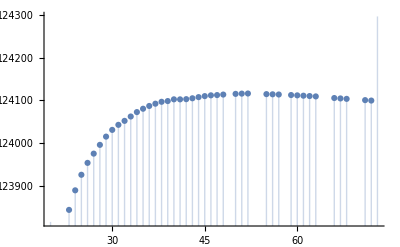

```mathematica
ListPlot[m[[2]],Joined->False, Filling->Axis]
```

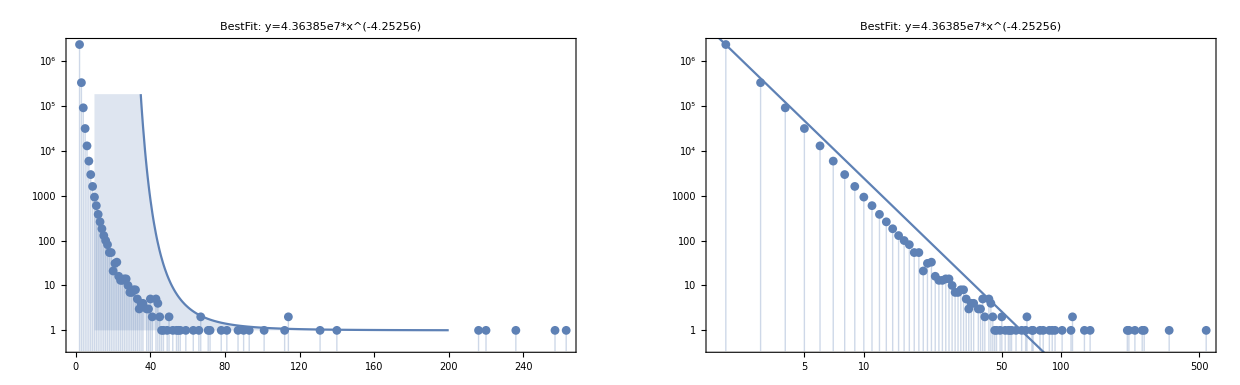

```mathematica
fitting = GraphicsGrid[{{fitPlot, loglogFitPlot}}]
```

```mathematica
Export[filename["powerlaw-fit.png"], fitting]
```

/home/agarcia_pc/Programming_pc/Bioinformatica/ICGC/results/to-plot/powerlaw-fit.png

```mathematica
λ = Total[ Map[#[[1]]*#[[2]]&, data]] / Total[ Map[#[[2]]&, data] ]
```

49971658/46429997

```mathematica
N[λ]
```

1.07628

```mathematica
Poisson = PDF[PoissonDistribution[λ], #]&
```

PDF[PoissonDistribution[λ],#1]&

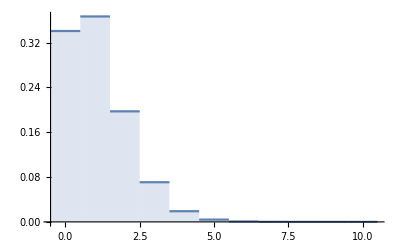

```mathematica
DiscretePlot[Poisson[k], {k, 0, 10}, ExtentSize->Full]
```

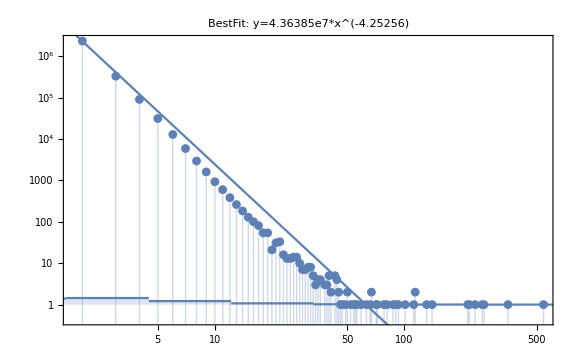

```mathematica
loglogFitPlot = Show[
ListLogLogPlot[data[[2;;]], Filling -> Axis],
LogLogPlot[fit[x],{x,1,542}],
DiscretePlot[Poisson[k], {k, 0, 10}, ExtentSize->Full],
Frame->True,
ImageSize->Large,
PlotLabel -> "BestFit: y=4.36385e7*x^(-4.25256)"
]
```

```mathematica
total = Total[Map[#[[2]]&, data]]
normalizedData = Map[{#[[1]], #[[2]]/total}&, data]
```

46429997

{{1,43637911/46429997},{2,2316229/46429997},{3,328046/46429997},{4,90285/46429997},{5,31236/46429997},{6,12826/46429997},{7,5876/46429997},{8,2945/46429997},{9,1603/46429997},{10,928/46429997},{11,598/46429997},{12,383/46429997},{13,261/46429997},{14,183/46429997},{15,129/46429997},{16,100/46429997},{17,81/46429997},{18,54/46429997},{19,54/46429997},{20,21/46429997},{21,31/46429997},{22,33/46429997},{23,16/46429997},{24,13/46429997},{25,13/46429997},{26,14/46429997},{27,14/46429997},{28,10/46429997},{29,7/46429997},{30,7/46429997},{31,8/46429997},{32,8/46429997},{33,5/46429997},{34,3/46429997},{35,4/46429997},{36,4/46429997},{38,3/46429997},{39,3/46429997},{40,5/46429997},{41,2/46429997},{43,5/46429997},{44,4/46429997},{45,2/46429997},{46,1/46429997},{47,1/46429997},{49,1/46429997},{50,2/46429997},{52,1/46429997},{54,1/46429997},{55,1/46429997},{56,1/46429997},{59,1/46429997},{63,1/46429997},{66,1/46429997},{67,2/46429997},{71,1/46429997},{72,1/46429997},{78,1/46429997},{81,1/46429997},{87,1/46429997},{90,1/46429997},{93,1/46429997},{101,1/46429997},{112,1/46429997},{114,2/46429997},{131,1/46429997},{140,1/46429997},{216,1/46429997},{220,1/46429997},{236,1/46429997},{257,1/46429997},{263,1/46429997},{352,1/46429997},{542,1/46429997}}

```mathematica
poisson =
```

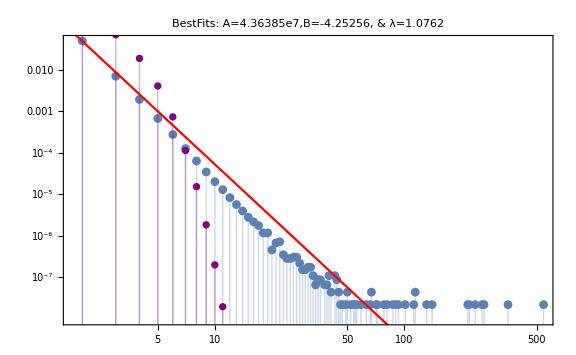

```mathematica
loglogFitPlot = Show[
ListLogLogPlot[normalizedData[[2;;]], Filling -> Axis],
LogLogPlot[fit[x]/total,{x,1,542}, PlotStyle->Red],
ListLogLogPlot[Map[Poisson, Range[100]],PlotStyle->Purple , Filling->Bottom],
Frame->True,
ImageSize->Large,
PlotLabel -> "BestFits: A=4.36385e7,B=-4.25256, & λ=1.0762"
]
```

```mathematica
fitPlot = Show[
ListPlot[normalizedData[[2;;]], Filling -> Axis],
Plot[fit[x]/total,{x,1,100}, PlotStyle->Red],
DiscretePlot[Poisson[k], {k, 0, 500}, ExtentSize->Scaled[0.5], PlotStyle->Purple, Filling->Axis],
Frame->True,
ImageSize->Large,
PlotLabel -> "BestFits: A=4.36385e7,B=-4.25256, & λ=1.0762"
]
```

-Graphics-

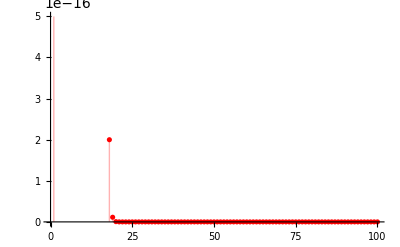

```mathematica
ListPlot[Partition[Riffle[Range[100],Map[PDF[PoissonDistribution[λ], #]&, Range[100]]],2], PlotStyle->Red, Filling->Axis]
```

```mathematica
fitting = GraphicsGrid[{{fitPlot, loglogFitPlot}}]
```

-Graphics-

```mathematica
Export[filename["powerlaw-fit.png"], fitting]
```

/home/agarcia_pc/Programming_pc/Bioinformatica/ICGC/results/to-plot/powerlaw-fit.png